# The Rigidity Package

## Setup and Initialization

The Rigidity package can be loaded by the following (so long as “Rigidity.m” is in the same directory as the notebook)

```mathematica
SetDirectory[NotebookDirectory[]];
<<Rigidity.m
```

If the file “Rigidity.m” is copied to your Mathematica’s “Application” directory,

```mathematica
FileNameJoin[{$UserBaseDirectory,"Applications"}]
```

via the command,

```mathematica
If[Not[FileExistsQ[FileNameJoin[{$UserBaseDirectory,"Applications","Rigidity.m"}]]],CopyFile[FileNameJoin[{NotebookDirectory[],"Rigidity.m"}],FileNameJoin[{$UserBaseDirectory,"Applications","Rigidity.m"}]]];
```

then “<<Rigidity.m” can be used in any notebook without any further initialization.

## Basic Operations

### Working with non-periodic frameworks

#### Framework data

A d-dimensional framework consists of a graph G = (V,E), and an embedding of the vertices V into R^d.

The Rigidity package uses adjacency lists to specify the underlying graph of a framework.  Each element of the list corresponds to an edge and contains three pieces of information.  The first is the pair of vertex indices that are joined by the edge.  The second is a labeling of the edge.  For non-periodic graphs, this label will be empty.  The final piece is a dummy slot which could be used to store, e.g. a spring constant.

Here is an example of the edge data for a triangular graph in 2D.

```mathematica
triangleedgedat={{{1,2},{},1},{{2,3},{},1},{{3,1},{},1}};
```

The embedding of the vertices is stored as a list of d-dimensional vectors.

```mathematica
trianglepos={{0,0},{1,0},{0,1}};
```

The function EdgeLengthsSq outputs the squared lengths of each of the edges:

```mathematica
EdgeLengthsSq[trianglepos,{},triangleedgedat]
```

{1,2,1}

#### Making pictures

The function PlotPacking can draw a picture of a 2D framework:

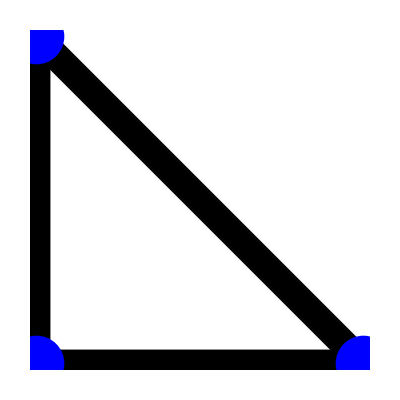

```mathematica
PlotPacking[trianglepos,triangleedgedat,{Blue,PointSize->.1},{Thickness->.05}]
```

Similarly, PlotPacking3D makes a picture of a 3D framework:

```mathematica
tetrahedronpos={{0,0,0},{1,0,0},{0,1,0},{0,0,1}};
tetrahedronedgedat={{{1,2},{},1},{{1,3},{},1},{{1,4},{},1},{{2,3},{},1},{{2,4},{},1},{{3,4},{},1}};
PlotPacking3D[tetrahedronpos,tetrahedronedgedat,{Blue,PointSize->.1},{Thickness->.05}]
```

-Graphics3D-

#### Rigidity matrices

The linear rigidity of a framework is completely determined by the properties of the rigidity matrix (often called the compatibility matrix).  This matrix is the Jacobian of the length function on the edges of the framework.

The function RigidityMatrix computes this matrix.  For 2D non-periodic frameworks it should be called as below.

```mathematica
triangleR=RigidityMatrix[{},trianglepos,{},triangleedgedat]
```

SparseArray[<8>,{3,6}]

```mathematica
Normal[triangleR]//MatrixForm
```

(-1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 1 | -1 | -1 | 1
0 | -1 | 0 | 0 | 0 | 1)

The space of floppy modes and self-stresses can then be computed via linear algebra:

```mathematica
NullSpace[triangleR]
```

{{-1,1,-1,0,0,1},{1,0,1,0,1,0},{1,0,1,1,0,0}}

```mathematica
NullSpace[Transpose[triangleR]]
```

{}

For a 3D non-periodic framework:

```mathematica
tetrahedronR=RigidityMatrix[{},tetrahedronpos,{},tetrahedronedgedat]
```

SparseArray[<18>,{6,12}]

```mathematica
Normal[tetrahedronR]//MatrixForm
```

(-1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | -1 | 0 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | -1 | 1)

The dynamical matrix and hence normal modes can be computed by multiplying the rigidity matrix by its transpose.  
One also needs to sandwich a diagonal matrix whose entries are the physical spring constants divided by the edge lengths squared.

```mathematica
tetrahedronD=Transpose[tetrahedronR].DiagonalMatrix[1/EdgeLengthsSq[tetrahedronpos,{},tetrahedronedgedat]].tetrahedronR;
```

```mathematica
Eigenvalues[tetrahedronD]
tetrahedronModes=Eigenvectors[tetrahedronD];
tetrahedronModes[[1]]
```

{4,5/2,5/2,1,1,1,0,0,0,0,0,0}

{-1/3,-1/3,-1/3,1,-1/3,-1/3,-1/3,1,-1/3,-1/3,-1/3,1}

The modes can be plotted with PlotPackingVec and PlotPackingVec3D

```mathematica
PlotPackingVec3D[tetrahedronpos,tetrahedronedgedat,.1tetrahedronModes[[1]]]
```

-Graphics3D-

### Periodic frameworks

#### Framework data

We will work with three example periodic frameworks, two in 2D, and one in 3D.  In each case, the position data is given as a list of coordinates for the vertices in a single fundamental domain.

```mathematica
chainpos={{1,0},{1/2,1/2}};
squarepos={{0,0},{1,0},{0,1},{1,1}};
cubepos={{0,0,0},{1,0,0},{0,1,0},{0,0,1},{1,1,0},{1,0,1},{0,1,1},{1,1,1}};
```

A periodic framework requires not just the positions of the vertices but also the basis vectors of the lattice.  This is input as a list of d vectors (b_1,...,b_d) for a d-periodic lattice:

```mathematica
chainbasis={{2,0}};
squarebasis={{2,0},{0,2}};
cubebasis={{2,0,0},{0,2,0},{0,0,2}};
```

The edge data of a periodic framework is encoded by giving a list of edges in a fundamental domain of the lattice.  Each edge is given as a list of three pieces of data.  The first piece is a (now ordered) pair of vertices (p_1,p_2), the second piece of data is (m_1,...,m_d), so that a vector pointing along the edge from p_1 to p_2 is (p_2-p_1)+m_1 b_1+...+m_d b_d, and the third is again a dummy slot.

```mathematica
chainedgedat={{{1,2},{0},1},{{1,2},{1},1}};
squareedgedat={{{1,2},{0,0},1},{{1,3},{0,0},1},{{2,4},{0,0},1},{{3,4},{0,0},1},{{2,1},{1,0},1},{{3,1},{0,1},1},{{4,2},{0,1},1},{{4,3},{1,0},1}};
cubeedgedat={{{1,2},{0,0,0},1},{{1,3},{0,0,0},1},{{1,4},{0,0,0},1},{{2,5},{0,0,0},1},{{2,6},{0,0,0},1},{{3,5},{0,0,0},1},{{3,7},{0,0,0},1},{{4,6},{0,0,0},1},{{4,7},{0,0,0},1},{{5,8},{0,0,0},1},{{6,8},{0,0,0},1},{{7,8},{0,0,0},1},
{{2,1},{1,0,0},1},{{5,3},{1,0,0},1},{{6,4},{1,0,0},1},{{8,7},{1,0,0},1},
{{3,1},{0,1,0},1},{{5,2},{0,1,0},1},{{7,4},{0,1,0},1},{{8,6},{0,1,0},1},
{{4,1},{0,0,1},1},{{6,2},{0,0,1},1},{{7,3},{0,0,1},1},{{8,5},{0,0,1},1}};
```

#### Making pictures

These frameworks can be drawn with the PlotPeriodicPacking and PlotPeriodicPacking3D functions.  We can plot multiple copies of each unit cell to better depict the periodicity if we wish:

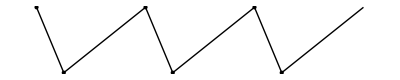

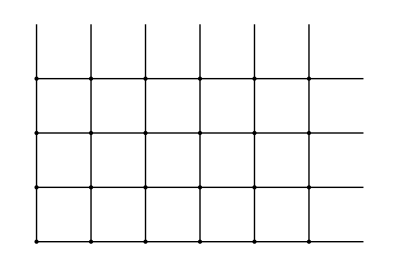

-Graphics3D-

```mathematica
PlotPeriodicPacking[chainpos,chainbasis,chainedgedat,{3}]
PlotPeriodicPacking[squarepos,squarebasis,squareedgedat,{3,2}]
PlotPeriodicPacking3D[cubepos,cubebasis,cubeedgedat,{5,2,3}]
```

#### Rigidity matrices

Two types of rigidity matrices can be computed.  The ordinary “Bloch”-type:

```mathematica
RigidityMatrix[{Exp[I k]},chainpos,chainbasis,chainedgedat]
```

SparseArray[<8>,{2,4}]

The “fixed-lattice” type:

```mathematica
RigidityMatrix[{1},chainpos,chainbasis,chainedgedat,True]
```

SparseArray[<10>,{2,6}]

```mathematica
Normal[%]
```

{{1/2,-1/2,-1/2,1/2,0,0},{-3/2,-1/2,3/2,1/2,3/2,1/2}}

#### Visualizing the modes in a 2D Brillouin zone

The function BandPlot makes contour plots of functions in the Brillouin zone.  Here is how to use it to look at various eigenmodes:

```mathematica
squarepos2=squarepos+RandomReal[{-.5,.5},{4,2}]
```

{{0.431252,0.286848},{0.626181,-0.077377},{-0.40911,1.45518},{0.628739,0.637853}}

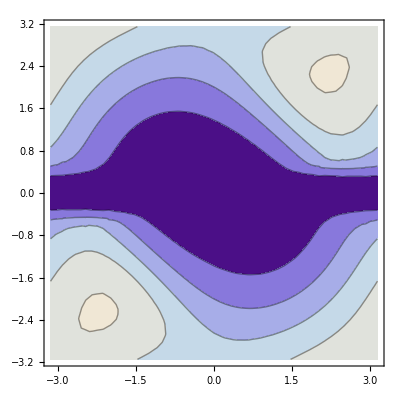

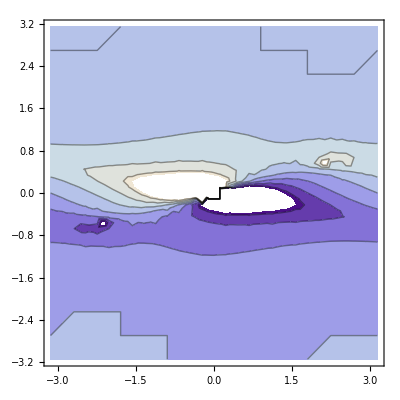

```mathematica
squareR=RigidityMatrix[{zx,zy},squarepos2,squarebasis,squareedgedatbalanced];
poly=Eigenvalues[ConjugateTranspose[squareR].squareR][[1]];

BandPlot[{zx,zy},Re[poly]]
BandPlot[{zx,zy},Im[poly]]
```

## Tools for laying out frameworks

### Frameworks from point configurations

### Built-in lattice framework functions

### Covers of periodic frameworks

Given a periodic framework it is often useful to construct coverings of this framework (i.e. a periodic framework whose unit cell consists of some number of copies of the original unit cell in different directions).

The functions MakePerLattice and MakePerLatticeEdges can do this:

```mathematica
squarecover=MakePerLattice[squarepos2,squarebasis,{3,2}];
squarecoveredgedat=MakePerLatticeEdges[squareedgedat,{3,2},True];
```

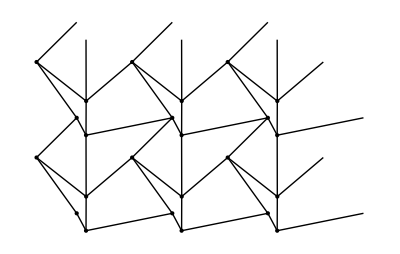

```mathematica
PlotPeriodicPacking[squarecover,squarebasis*{3,2},squarecoveredgedat]
```

To truncate the periodic edges at the boundary, use the following (this is the default behavior if the final argument is omitted):

```mathematica
squarecovernonperiodicedgedat=MakePerLatticeEdges[squareedgedat,{3,2},False];
```

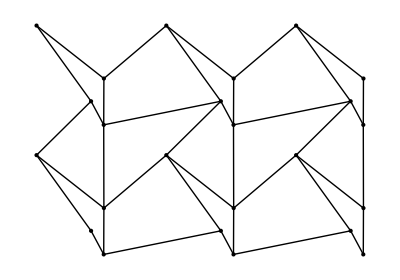

```mathematica
PlotPacking[squarecover,squarecovernonperiodicedgedat]
```

### Cutting and gluing frameworks

## Other computations

### Boundary conditions and pinning / Pebble basis modes

If one wants to compute the floppy modes of a system with additional constraints, this can be done by adjoining new rows to the rigidity matrix.

```mathematica
trianglepin1xR=Join[triangleR,{{1,0,0,0,0,0}}]
```

{{-1,0,1,0,0,0},{0,0,1,-1,-1,1},{0,-1,0,0,0,1},{1,0,0,0,0,0}}

```mathematica
NullSpace[trianglepin1xR]
```

{{0,-1,0,-1,0,-1},{0,0,0,1,-1,0}}

#### Boundary vertex indices

Often additional constraints on a framework derive from boundary conditions.  The function BoundaryVerts can be used to get boundary vertex indices of frameworks derived from MakePerLattice and MakePerLatticeEdges

One inputs the edge data, the size of the covering, and the vertex indices (in a single unit cell) that go on each face.  Since the overall structure is that of a hypercube, there is a “front” and “back” face per dimension: for example if the basis vectors are {{2,0},{0,2}}, then the list of faces is {{left, right},{bottom,top}}:

```mathematica
squarebv=BoundaryVerts[squareedgedat,{3,2},{{{1,3},{2,4}},{{1,2},{3,4}}}]
```

{{{1,3,5,7},{18,20,22,24}},{{1,2,9,10,17,18},{7,8,15,16,23,24}}}

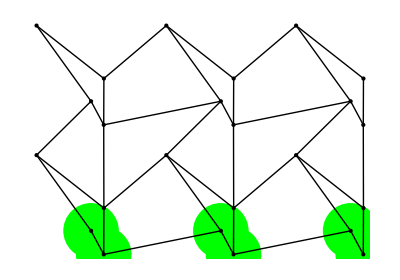

```mathematica
Show[PlotPacking[squarecover[[squarebv[[2,1]]]],{},{PointSize->.1,Green}],PlotPacking[squarecover,squarecovernonperiodicedgedat]]
```

#### Pebble modes

Once we have determined a set of boundary vertices, we can pin them by adding new constraints to the system.  The linearizations of these constraints can be added directly to the rigidity matrix as new rows, generated by ConstraintRows.  This function takes as input first the total number of vertices in the system, then a list of vertex indices, and finally a template for the constraints at each pinned vertex. Then ConstraintRows outputs a number of rows that can be directly added to the rigidity matrix:

```mathematica
newconstraints1=ConstraintRows[Length[squarecover],squarebv[[2,2]],{1,0}];
newrigmat=Join[RigidityMatrix[{},squarecover,{},squarecovernonperiodicedgedat],newconstraints1];
Length[NullSpace[newrigmat]]
```

4

There’s an interpretation for the pebbles in the pebble game as added constraints which cause an independent framework to become isostatic in the sense of being minimally pinned down.

Given such a pinning, if we remove one constraint, the system gains a single floppy mode.  Thus we can associate floppy modes with pin constraints of such a minimally pinned system.  These are what I call the pebble modes of the system.

### Linear response and stresses

### Local “circle” modes

### Brillouin zone / topological invariants

Kane and Lubensky [KL14] defined some quantities that determine the edge behavior of isostatic lattices.

#### Net dipole

In order to ensure that the quantities further below make sense, we must check what the contribution of our choice of fundamental domain is.  This is given by the “net dipole” r_0:

```mathematica
NetDipole[squarepos,squarebasis,squareedgedat]
NetDipole[cubepos,cubebasis,cubeedgedat]
```

{-1,-1}

{-2,-2,-2}

With a different choice of the edge data, this can often be made to vanish.

```mathematica
squareedgedatbalanced={{{1,2},{0,0},1},{{1,3},{0,0},1},{{2,4},{0,0},1},{{3,4},{0,0},1},{{1,2},{-1,0},1},{{1,3},{0,-1},1},{{4,2},{0,1},1},{{4,3},{1,0},1}};
NetDipole[squarepos,squarebasis,squareedgedatbalanced]
```

{0,0}

#### Visualizing the determinant in a 2D Brillouin zone

BandPlot may be used to make a contour plot of log|det R| in the Brillouin zone.

Note the use of the function NRigidityMatrix which forces Mathematica to evaluate the determinant only after numerical values are inserted for zx, zy, which can improve the numerical accuracy.

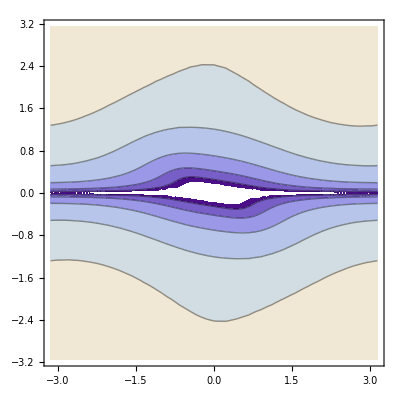

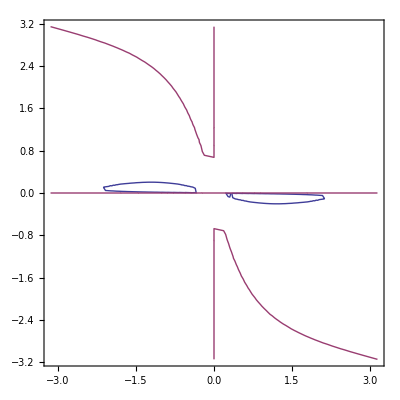

```mathematica
poly=Det[NRigidityMatrix[{zx,zy},squarepos2,squarebasis,squareedgedatbalanced]];

BandPlot[{zx,zy},Log[Abs[poly]]]
BandPlot[{zx,zy},{Re[poly]==0,Im[poly]==0}]
```

#### Winding numbers / polarization

KLWinding computes the winding of the phase of the det R on different paths in the Brillouin zone.

```mathematica
KLWinding[{zx,zy},squarepos,squarebasis,squareedgedatbalanced,{zx->Exp[I(.3+.01Cos[ t])],zy->Exp[I(.3+.01Sin[ t])]},t]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {5.32588}. NIntegrate obtained 2.61075×10^-17 and 1.71501×10^-15 for the integral and error estimates.

4.15514×10^-18

The function KLPolarization computes a topological polarization vector by putting together the winding along orthogonal cycles in the Brillouin zone starting at a given point cycleorigin:

```mathematica
KLPolarization[squarepos2,squarebasis,squareedgedatbalanced,{-1,-1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$39986 near {t$39986} = {4.93318}. NIntegrate obtained 1.49186×10^-16 and 6.75226×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t$39986 near {t$39986} = {6.278104214559740302477319762175511641544289886951446533203125}. NIntegrate obtained 1.97042×10^-10 and 7.03682×10^-6 for the integral and error estimates.

{2.37437×10^-17,3.13603×10^-11}

## References

[KL14] C.L. Kane and T.C. Lubensky, Nature Physics 2014